```mathematica
(*a set of observable transitions should read: { {{s(l), t(l), Subscript[r, l]}, {s(l̄), t(l̄), Subscript[r, l̄]}}, ... } *)
(*an event reads: x = {{s(l), t(l), Subscript[r, l]}, ...} for all l ∈ θ^-1 x*)

(*for aesthetic purposes, sorry*)
Needs["MaTeX`"]
SetDirectory[NotebookDirectory[]];
magentaviva = RGBColor[{190,52,85}/255];
pageantblue = RGBColor[{31,44,67}/255];
castletongreen = RGBColor[{28,88,64}/255];
sepia = RGBColor[{122,78,13}/255];
mark = #1 &@@@ Graphics`PlotMarkers[];

(*stationary distribution achieved by a generator*)
SteadyState[mat_] := Module[{pss},
	pss = Table[(-1)^j Det[ Drop[mat,{2},{j}] ], {j,Length@mat}];
	pss = pss/Total[pss]
]

(*define log(0/0) = 0*)
SmartLog[a_, b_] := If[ PossibleZeroQ[Chop[a]] ∧ PossibleZeroQ[Chop[b]], 0, Log[a/b]]

(*entropy production rate, "set" has to include ALL transitions*)
EPR[R_, set_] := Module[{ps},
	ps = SteadyState[R];
	Sum[( ps[[s[[1,1]]]]s[[1,3]] - ps[[s[[2,1]]]]s[[2,3]] ) SmartLog[s[[1,3]], s[[2,3]]], {s,set}]
]

(*traffic of a set of transitions*)
Kfun[set_, pss_] := Total[#3 pss[[#1]] &@@@ Flatten[set,1]]

(*survival matrix*)
Smatrix[R_, set_] := Module[{S},
	S = R;
	( S[[#2,#1]] -= #3 ) &@@@ Flatten[set,1];
	S
]

(*matrix Γ of an event x*)
Γmatrix[x_, pss_] := Module[{Γ},
	Γ = (Table[0, {i,Length[pss]}, {j,Length[pss]}]);
	(Γ[[#2,#1]] += #3) &@@@ x;
	Kfun[{x},pss]^-1 Γ
]

(*convenient functions for the statistics of events*)
Px[pss_,transitions_,R_][x_] := Kfun[{x},pss]/Kfun[transitions,pss];
Px2Gx1[pss_,transitions_,R_][x1_,x2_] := -Kfun[{x2},pss]Total[Γmatrix[x2,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x1,pss].pss]
Px2tGx1[pss_,transitions_,R_][x1_,x2_,t_] := Kfun[{x2},pss]Total[Γmatrix[x2,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x1,pss].pss]

(*Fermi-Dirac and Bose-Einstein statistics*)
FD[ϵ_,β_]:=(1+Exp[β ϵ])^-1;
BE[ϵ_,β_]:=(Exp[β ϵ] - 1)^-1;
```

## example of functions usage

defining the double QD model

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={4,3.5,1,7};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,5};
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
σ= pss[[4]](w0100r1 Log[w0100r1/w0001r1]+w0100r2 Log[w0100r2/w0001r2]+w1000r3 Log[w1000r3/w0010r3]+w1000r4 Log[w1000r4/w0010r4])+pss[[3]](w0010r3 Log[w0010r3/w1000r3]+w0010r4 Log[w0010r4/w1000r4]+w1110r1 Log[w1110r1/w1011r1]+w1110r2 Log[w1110r2/w1011r2])+pss[[2]](w1011r1 Log[w1011r1/w1110r1]+w1011r2 Log[w1011r2/w1110r2]+w0111r3 Log[w0111r3/w1101r3]+w0111r4 Log[w0111r4/w1101r4])+pss[[1]](w0001r1 Log[w0001r1/w0100r1]+w0001r2 Log[w0001r2/w0100r2]+w1101r3 Log[w1101r3/w0111r3]+w1101r4 Log[w1101r4/w0111r4])//N;
```

entropy production rate

```mathematica
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
{σ,EPR[R,transitions]}
```

{15.2455,15.2455}

defining the multifilar events

```mathematica
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
```

survival matrix from the function and also from R - 𝒦 Γ

```mathematica
Smatrix[R,{x1plus}]//MatrixForm
(R-Kfun[{x1plus},pss]Γmatrix[x1plus, pss])-Smatrix[R,{x1plus}]//MatrixForm//Chop
```

(-11.774 | 10.4494 | 0. | 4.08787
9.55061 | -25.7811 | 0.146561 | 0.
0. | 15.3318 | -4.20039 | 16.4679
2.22336 | 0. | 3.53214 | -30.2445)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

sum of traffic rates is the total traffic rate

```mathematica
Total[Kfun[{#},pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
Kfun[transitions,pss]
```

9.64768

9.64768

State after an event

```mathematica
Γmatrix[x3minus,pss].pss
```

{0.20145,0.,0.,0.79855}

P(ℓ, t | x)

```mathematica
w1101r3 (MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss)[[1]]//Simplify
```

0.00943792 ⅇ^(-11.774 t)

P(x’, t | x)

```mathematica
Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].MatrixExp[t Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2tGx1[pss,transitions,R][x3minus,x4plus,t]//Simplify//Chop
```

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

10.3555 ⅇ^(-30.2445 t)+1.91453 ⅇ^(-11.774 t)

P (x' | x) and its normalization

```mathematica
-Kfun[{x4plus},pss]Total[Γmatrix[x4plus,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]//Simplify//Chop
Px2Gx1[pss,transitions,R][x3minus,x4plus]
Total[-Kfun[{#},pss]Total[Γmatrix[#,pss].Inverse[Smatrix[R,transitions]].Γmatrix[x3minus,pss].pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.504999

0.504999

1.

P (x)

```mathematica
Kfun[{x1plus},pss]/Kfun[transitions,pss]
Px[pss,transitions,R][x1plus]
Total[Kfun[{#},pss]/Kfun[transitions,pss]&/@{x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus}]
```

0.124621

0.124621

1.

## DQD

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,transitions,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];`
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

AppendTo[vec,Chop@{A12,A34,σ,σzk,σti,Dx,Dtt}];
,{x,3,7,.1}]
```

```mathematica
{Px2Gx1[pss,Xspace,R][x1plus,x2minus],Px[pss,Xspace,R][x1plus],Px2Gx1[pss,Xspace,R][x2plus,x1minus],Px[pss,transitions,R][x2plus]}
{-Kfun[{x2minus},pss],Tr[Γmatrix[x2minus,pss].Inverse[S].Γmatrix[x1plus,pss].pss]}
{-Kfun[{x1minus},pss],Tr[Γmatrix[x1minus,pss].Inverse[S].Γmatrix[x2plus,pss].pss]}
{Log@((w0100r1 w0001r2 +w1110r1 w1011r2)/(w0100r2 w0001r1 +w1110r2 w1011r1)),μ1-μ2}
```

{0.0211175,0.0912262,0.229574,0.0620054}

{-0.17682,-0.119429}

{-1.75153,-0.131071}

{-2.,-2.}

```mathematica
a12empirical
```

-2.

```mathematica
leg=Column[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],PointLegend[{magentaviva,pageantblue},MaTeX[#,FontSize->15]&/@{"\\sigma_\\text{ti}","\\sigma_\\text{zk}"},LegendMarkers->mark[[1;;2]]]},Automatic,-.3];
Show[
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->Black,PlotRange->All],
ListPlot[{#1,#5}&@@@vec,PlotStyle->{magentaviva,Opacity[.7]},PlotMarkers->{mark[[1]],12}],
ListPlot[{#1,Total[#4[[;;8]]]}&@@@vec,PlotStyle->{pageantblue,Opacity[.7]},PlotMarkers->{mark[[2]],12}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.4,.75}]]},ImageSize->220,AspectRatio->0.9,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-2,2},All}]
```

-Graphics-

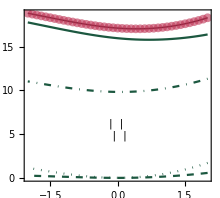

```mathematica
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->15]},LegendMarkers->(mark[[1]])],LineLegend[{Dashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(1)}",FontSize->15]},LegendMarkerSize->22],LineLegend[{Dotted,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(2)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{DotDashed,castletongreen},{MaTeX["\\sigma_\\text{zk}^{(3)}",FontSize->15]},LegendMarkerSize->22],
LineLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{(4)}",FontSize->15]},LegendMarkerSize->22]},3,Spacings->{0,-1}];
plotDDEPR=Show[
ListLinePlot[{#1,#3}&@@@vec,PlotStyle->{Black,Thick},PlotRange->All],
ListPlot[{#1,#5}&@@@vec,PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],9}],
ListLinePlot[{#1,Total[#4[[;;2]]]}&@@@vec,PlotStyle->{castletongreen,Dashed}],
ListLinePlot[{#1,Total[#4[[;;4]]]}&@@@vec,PlotStyle->{castletongreen,Dotted}],
ListLinePlot[{#1,Total[#4[[;;6]]]}&@@@vec,PlotStyle->{castletongreen,DotDashed}],
ListLinePlot[{#1,Total[#4[[;;8]]]}&@@@vec,PlotStyle->{castletongreen}],
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.5,.3}]]},ImageSize->220,AspectRatio->0.9,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->{{-2,2},All},ImagePadding->{{17,5},{40,5}}]
```

```mathematica
{Γ1,Γ2,Γ3,Γ4}={11,5,7,13};
{μ1,μ2,μ3,μ4}={5,1,6,1};
{β1,β2,β3,β4}={1,1,1,1};
{ϵu,ϵd,Δϵ}={2,1,3};
vec2={};Do[
μ2=x;
w0111r3=Γ3 (1-FD[ϵd+Δϵ-μ3,β3]);w1101r3=Γ3 FD[ϵd+Δϵ-μ3,β3];
w0111r4=Γ4 (1-FD[ϵd+Δϵ-μ4,β4]);w1101r4=Γ4 FD[ϵd+Δϵ-μ4,β4];
w0100r1=Γ1 FD[ϵu-μ1,β1];w0001r1=Γ1 (1-FD[ϵu-μ1,β1]);
w0100r2=Γ2 FD[ϵu-μ2,β2];w0001r2=Γ2 (1-FD[ϵu-μ2,β2]);
w1110r1=Γ1 FD[ϵu+Δϵ-μ1,β1];w1011r1=Γ1(1- FD[ϵu+Δϵ-μ1,β1]);
w1110r2=Γ2 FD[ϵu+Δϵ-μ2,β2];w1011r2=Γ2(1- FD[ϵu+Δϵ-μ2,β2]);
w1000r3=Γ3 FD[ϵd-μ3,β3];w0010r3=Γ3 (1-FD[ϵd-μ3,β3]);
w1000r4=Γ4 FD[ϵd-μ4,β4];w0010r4=Γ4 (1-FD[ϵd-μ4,β4]);
(*01,11,10,00*)
R=({{0, w0111r3+w0111r4, 0, w0100r1+w0100r2}, {w1101r3+w1101r4, 0, w1110r1+w1110r2, 0}, {0, w1011r1+w1011r2, 0, w1000r3+w1000r4}, {w0001r1+w0001r2, 0, w0010r3+w0010r4, 0}});
R=(R-DiagonalMatrix[Total[R]]);pss=SteadyState[R];
x1plus={{4,1,w0100r1},{3,2,w1110r1}};x1minus={{1,4,w0001r1},{2,3,w1011r1}};rev[x1plus]=x1minus;rev[x1minus]=x1plus;
x2plus={{4,1,w0100r2},{3,2,w1110r2}};x2minus={{1,4,w0001r2},{2,3,w1011r2}};rev[x2plus]=x2minus;rev[x2minus]=x2plus;
x3plus={{4,3,w1000r3},{1,2,w1101r3}};x3minus={{3,4,w0010r3},{2,1,w0111r3}};rev[x3plus]=x3minus;rev[x3minus]=x3plus;
x4plus={{4,3,w1000r4},{1,2,w1101r4}};x4minus={{3,4,w0010r4},{2,1,w0111r4}};rev[x4plus]=x4minus;rev[x4minus]=x4plus;
Xspace={x1plus,x1minus,x2plus,x2minus,x3plus,x3minus,x4plus,x4minus};
transitions={{{4,1,w0100r1},{1,4,w0001r1}},{{4,1,w0100r2},{1,4,w0001r2}},{{3,2,w1110r1},{2,3,w1011r1}},{{3,2,w1110r2},{2,3,w1011r2}},{{1,2,w1101r3},{2,1,w0111r3}},{{1,2,w1101r4},{2,1,w0111r4}},{{4,3,w1000r3},{3,4,w0010r3}},{{4,3,w1000r4},{3,4,w0010r4}}};
σ=N@EPR[R,transitions];
S=Smatrix[R,Xspace];Z=N@Kfun[Xspace,pss];

(*σzk*)
σzk=Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace;

(*σti*)
A12=β1 μ1-β2 μ2;A34=β3 μ3-β4 μ4;
a12empirical=Log[(Px2Gx1[pss,Xspace,R][x1plus,x2minus]Px[pss,Xspace,R][x1plus])/(Px2Gx1[pss,Xspace,R][x2plus,x1minus]Px[pss,Xspace,R][x2plus])];
a34empirical=Log[(Px2Gx1[pss,Xspace,R][x3plus,x4minus]Px[pss,Xspace,R][x3plus])/(Px2Gx1[pss,Xspace,R][x4plus,x3minus]Px[pss,Xspace,R][x4plus])];
σti=Z(Px[pss,Xspace,R][x1plus]-Px[pss,Xspace,R][x1minus])a12empirical+Z(Px[pss,Xspace,R][x3plus]-Px[pss,Xspace,R][x3minus])a34empirical;

(*observing reservoir 1*)
trans1={x1plus,x1minus};
Dx=0;Dtt=0;
Do[
Px1x2=Px2Gx1[pss,trans1,R][x1,x2]Px[pss,trans1,R][x1];
Px2rx1r=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]Px[pss,trans1,R][rev[x2]];
a=Px2Gx1[pss,trans1,R][x1,x2]//Simplify//Chop;
b=Px2Gx1[pss,trans1,R][rev[x2],rev[x1]]//Simplify//Chop;
at=If[PossibleZeroQ[a],∞,(Px2tGx1[pss,trans1,R][x1,x2,t])/a//Simplify//Chop];
bt=If[PossibleZeroQ[b],∞,(Px2tGx1[pss,trans1,R][rev[x2],rev[x1],t])/b//Simplify//Chop];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
Dtt+=If[PossibleZeroQ[a]∨PossibleZeroQ[b],0,Px1x2 Quiet@NIntegrate[at SmartLog[at,bt],{t,0,∞}]];
,{x1,Xspace[[;;2]]},{x2,Xspace[[;;2]]}];

AppendTo[vec2,Chop@{A12,A34,σ,σzk,σti,Dx,Dtt}];
,{x,4.5,5.5,.025}]
```

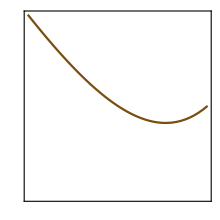
{-Graphics--Graphics-,-Graphics-}

```mathematica
size=220;ar=1;
leg=Column[{LineLegend[{pageantblue,sepia},MaTeX[#,FontSize->14]&/@{"D_x","D_t\\ [10^{-4}]"}]},Automatic,-.3];
plot1=ListLinePlot[{#1,#6}&@@@vec2,PlotStyle->pageantblue,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{True,True,True,False},FrameStyle->{Black,pageantblue,Black,Black},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.6,.77}]]}];
plot2=ListLinePlot[{#1,#7 10^4}&@@@vec2,PlotStyle->sepia,ImagePadding->{{22,20},{40,5}},Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Black,Black,Black,sepia},ImageSize->size,AspectRatio->ar,LabelStyle->{Black,FontFamily->"Times"},FrameLabel->{MaTeX["A_{12}",FontSize->14],""}];
plotDDD=Overlay[{plot1,plot2}];
{plotDDD,plotDDEPR}
```

```mathematica
Export["plot_DD_EPR.png",plotDDEPR,"PNG",ImageResolution->600]
Export["plot_DD_Dxt.png",plotDDD,"PNG",ImageResolution->600]
```

plot_DD_EPR.png

plot_DD_Dxt.png

## Brusselator

### analytical approximation

The state space is truncated with a fixed N_max and all other calculations are analytical

```mathematica
Nmax=20;Nx[Nmax_][i_]:=Floor[(i-1)/(Nmax+1)];Ny[Nmax_][i_]:=Mod[i-1,Nmax+1];
{k1,km1,k2,km2,k3,km3}={3,2,2,3,3,1};{A,B}={9,10};V=2;
```

Builiding the generator:

```mathematica
(*yp = +B, xp = -A, y = inner*)
ruleyp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[k2 B],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruleym=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[km2 Ny[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexp=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[k1 A],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulexm=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j],{i,j}->N[km1 Nx[Nmax][j]],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
rulex=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]-1∧Ny[Nmax][i]==Ny[Nmax][j]+1,{i,j}->N[km3(Nx[Nmax][j](Nx[Nmax][j]-1)(Nx[Nmax][j]-2))/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
ruley=Flatten@Table[If[Nx[Nmax][i]==Nx[Nmax][j]+1∧Ny[Nmax][i]==Ny[Nmax][j]-1,{i,j}->N[k3(Nx[Nmax][j](Nx[Nmax][j]-1)Ny[Nmax][j])/V^2],##&[]],{i,(Nmax+1)^2},{j,(Nmax+1)^2}];
Rsp1=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley]];
TRsp=Total[Rsp1];
ruleesc=Table[{i,i}->-TRsp[[i]],{i,(Nmax+1)^2}];
Rsp=SparseArray[Join[ruleyp,ruleym,rulexp,rulexm,rulex,ruley,ruleesc]];
ByteCount[Rsp]/10^6//N
```

0.051312

Stationary distribution

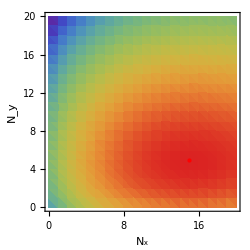
{-Graphics-,-Graphics3D-}

```mathematica
<<ComputationalGeometry`
pss=SteadyState[Rsp];
pssNxNy=Table[{Nx[Nmax][i],Ny[Nmax][i],pss[[i]]},{i,Length@pss}];
points={#1,#2}&@@@pssNxNy;zval=#3&@@@pssNxNy;
tri=DelaunayTriangulation[points];
tests=And@@Thread[zval[[#1]]>zval[[#2]]]&@@@tri;
maxima=Pick[points,tests];
{ListDensityPlot[ArrayFlatten[{{points,List/@zval}}],Epilog->{Red,PointSize[Large],Point[maxima]},PlotRange->All,ImageSize->250,FrameStyle->Black,FrameLabel->{"N_x","N_y"},ColorFunction->"Rainbow",ScalingFunctions->{None,None,"Log"}],ListPlot3D[pssNxNy,PlotRange->All,AxesLabel->{"N_x","N_y","p_st"},ImageSize->300,AxesStyle->Black]}
```

Defining the multifilar events

```mathematica
(*yp = +B, xp = +A, y = inner*)
xAplus={#1[[2]],#1[[1]],#2}&@@@rulexp;xAminus={#1[[2]],#1[[1]],#2}&@@@rulexm;rev[xAplus]=xAminus;rev[xAminus]=xAplus;
xBplus={#1[[2]],#1[[1]],#2}&@@@ruleyp;xBminus={#1[[2]],#1[[1]],#2}&@@@ruleym;rev[xBplus]=xBminus;rev[xBminus]=xBplus;
xIplus={#1[[2]],#1[[1]],#2}&@@@ruley;xIminus={#1[[2]],#1[[1]],#2}&@@@rulex;rev[xIplus]=xIminus;rev[xIminus]=xIplus;
Xspace={xAplus,xAminus,xBplus,xBminus,xIplus,xIminus};
transitions=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}],Transpose[{xIplus,xIminus}]];
Ssp=Smatrix[Rsp,transitions];
Z=Kfun[transitions,pss];
σ=EPR[Rsp,transitions];
```

The estimator σ_zk when chemostats A and B are monitored:

```mathematica
(*from A and B*)
transAB=Join[Transpose[{xAplus,xAminus}],Transpose[{xBplus,xBminus}]];
Ssp=Smatrix[Rsp,transAB];
Z=Kfun[transAB,pss];
σzk=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace[[;;4]]];
σzkB=Total[Z( Kfun[{#},pss]/Z SmartLog[Kfun[{#},pss],Kfun[{rev[#]},pss]])&/@Xspace[[3;;4]]];
{Δμ=Log[(B k2 km1 k3)/(A km2 k1 km3)]//N,σ,σzk,σzkB}
```

{0.393043,1.6354,1.60214,0.970521}

The detector D_x

```mathematica
(*observing chemostats A and B*)
trans1={xAplus,xAminus,xBplus,xBminus};
Dx=0;
Do[
Px1x2=Px2Gx1[pss,trans1,Rsp][x1,x2]Px[pss,trans1,Rsp][x1];
Px2rx1r=Px2Gx1[pss,trans1,Rsp][rev[x2],rev[x1]]Px[pss,trans1,Rsp][rev[x2]];
Dx+=Px1x2 SmartLog[Px1x2,Px2rx1r];
,{x1,Xspace[[;;4]]},{x2,Xspace[[;;4]]}];
Dx
```

0.0354987

```mathematica
Plα=Kfun[{xAminus},pss]/Kfun[transitions,pss] Kfun[{xIplus},pss]Kfun[{xBplus},pss]Total[Γmatrix[xIplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xBplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xAminus,pss].pss];
Plαr=Kfun[{xIminus},pss]/Kfun[transitions,pss] Kfun[{xAplus},pss]Kfun[{xBminus},pss]Total[Γmatrix[xAplus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xBminus,pss].Inverse[Smatrix[Rsp,transitions]].Γmatrix[xIminus,pss].pss];
{Δμ,Log[Plα/Plαr]}
```

{0.393043,0.393043}

### plot from simulation data

```mathematica
data=Import["bruss_simulation_results.txt","Table"];
```

```mathematica
aff_mean,epr_mean,epr_std,σzkB_mean,σzkB_std,σzk_mean,σzk_std,σti_mean,σti_std,Dx_mean,Dx_std,Dt_mean,Dt_std
```

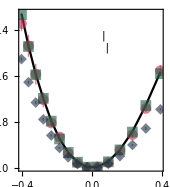

```mathematica
leg=Multicolumn[{LineLegend[{Black},{MaTeX["\\sigma",FontSize->15]}],
PointLegend[{magentaviva},{MaTeX["\\sigma_\\text{ti}",FontSize->15]},LegendMarkers->(mark[[1]])],PointLegend[{castletongreen},{MaTeX["\\sigma_\\text{zk}^{A,B}",FontSize->15]},LegendMarkers->(mark[[2]])],
PointLegend[{pageantblue},{MaTeX["\\sigma_\\text{zk}^{B}",FontSize->15]},LegendMarkers->(mark[[3]])]},2,Spacings->{0,-1}];
plotBrussEPR=Show[{ListLinePlot[{#1,#2}&@@@data,PlotStyle->Black],
ListPlot[{#1,Around[#8,#9]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{magentaviva,Opacity[.6]},PlotMarkers->{mark[[1]],11}],
ListPlot[{#1,Around[#6,#7]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{castletongreen,Opacity[.6]},PlotMarkers->{mark[[2]],11}],
ListPlot[{#1,Around[#4,#5]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{pageantblue,Opacity[.6]},PlotMarkers->{mark[[3]],11}]},
Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.6,.8}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->All,ImagePadding->{{25,5},{40,5}}]
```

```mathematica
leg=Column[{PointLegend[{pageantblue},{MaTeX["D_x",FontSize->14]},LegendMarkers->(mark[[1]])],PointLegend[{sepia},{MaTeX["D_t",FontSize->14]},LegendMarkers->(mark[[2]])]},Automatic,-.3];
plotBrussD=Show[{ListLinePlot[{#1,Around[#10,#11]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{pageantblue,Opacity[.6]},PlotMarkers->{mark[[1]],11}],ListLinePlot[{#1,Around[#12,#13]}&@@@data,IntervalMarkers->"Bars",PlotStyle->{sepia,Opacity[.6]},PlotMarkers->{mark[[2]],11}]},Frame->True,FrameStyle->Black,FrameLabel->{MaTeX["\\Delta\\mu",FontSize->14],""},Epilog->{Inset[leg,Scaled[{.6,.8}]]},ImageSize->170,AspectRatio->1.1,LabelStyle->{Black,FontFamily->"Times"},Axes->False,PlotRange->All,ImagePadding->{{25,5},{40,5}}]
```

-Graphics-

```mathematica
Export["plot_Bruss_EPR.png",plotBrussEPR,"PNG",ImageResolution->600]
Export["plot_Bruss_Dxt.png",plotBrussD,"PNG",ImageResolution->600]
```

## Gershgorin circles

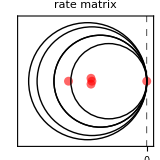
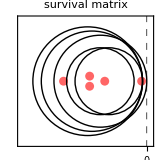

```mathematica
R={{0,1,2,3,4},{1,0,4,3,2},{5,4,0,3,2},{5,4,1,0,3},{3,4,2,2,0}}/10;
R=R-DiagonalMatrix[Total[R]];
S=R;(S[[#2,#1]]=0)&@@@{{1,2},{2,1},{3,4},{4,3}};
eigsR=Eigenvalues[R]//N;
eigsS=Eigenvalues[S]//N;
gcR=Table[{R[[i,i]],Total@Drop[R[[;;,i]],{i}]},{i,Length@R}];
gcS=Table[{S[[i,i]],Total@Drop[S[[;;,i]],{i}]},{i,Length@R}];

a=ListPlot[{Re[#],Im[#]}&/@eigsR,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcR),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times"},PlotLabel->Style["rate matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
b=ListPlot[{Re[#],Im[#]}&/@eigsS,PlotStyle->{Red,PointSize->.04,Opacity[0.6]},Epilog->((Circle[{#1,0},#2])&@@@gcS),PlotRange->{{-3,.1},{-1.5,1.5}},ImageSize->160,LabelStyle->{Black,FontFamily->"Times"},PlotLabel->Style["survival matrix",FontFamily->"Times New Roman"],LabelStyle->Black,AspectRatio->1,Frame->True,FrameStyle->Black,GridLines->{{0},{}},GridLinesStyle->Directive[Dashed,Black],FrameLabel->{MaTeX["\\mathsf{Re}(\\lambda)",FontSize->12],MaTeX["\\mathsf{Im}(\\lambda)",FontSize->12]},FrameTicks->{None,{{0},None}}];
{a,b}
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["gershgorin_R.png",a,"PNG",ImageResolution->500]
Export["gershgorin_S.png",b,"PNG",ImageResolution->500]
```

gershgorin_R.png

gershgorin_S.png